```mathematica
Table[ChromaticPolynomial[EmbedGraphInPlantri8b[k],4],{k,alfa1s}]
```

{72,192,0,192,72}

```mathematica
Table[PlanarGraphQ[EmbedGraphInPlantri8b[k]],{k,alfa1s}]
```

{False,False,False,False,False}

```mathematica
alfa1s
```

{36166,31738,29608,36112,31714}

```mathematica
Table[ShowGraph5Least[k],{k,alfa1s}]
```

{-Graphics-361660,-Graphics-317380,-Graphics-296080,-Graphics-361120,-Graphics-317140}

```mathematica
ChromaticPolynomial[EmbedGraphInPlantri8b[29608],4]
```

0

```mathematica
emb=EmbedGraphInPlantri8b[29608]
```

```mathematica
emb2=EmbedGraphInPlantri8b[31714]
```

```mathematica
FindClique[emb]
```

{{12,13,7}}

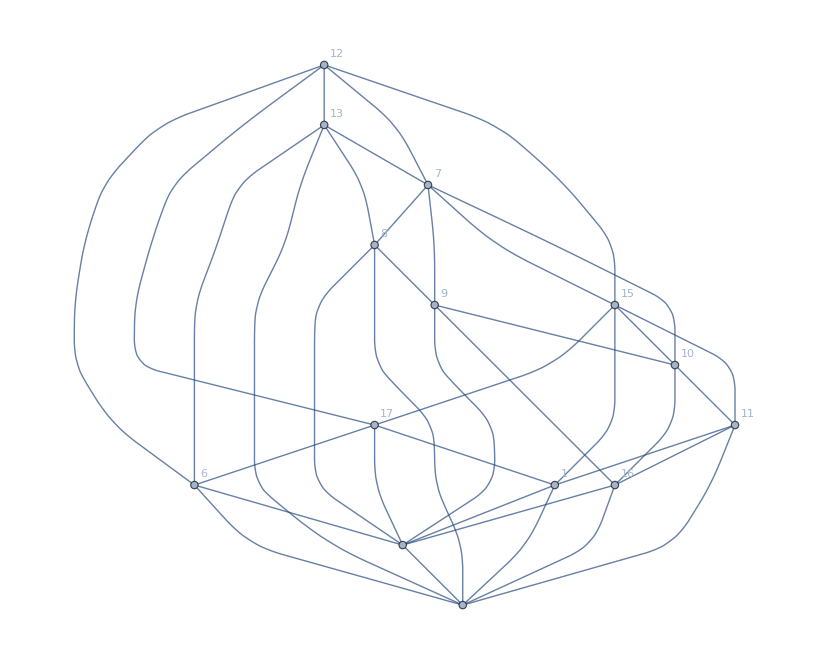

```mathematica
Graph[emb,GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
FindFullFormula5[emb]//Length
```

1586

```mathematica
1586/120
```

793/60

```mathematica
ChromaticPolynomial[EmbedGraphInPlantri8b[29608],5]/120
```

1586

```mathematica
CompleteBaseCoeff[ ChromaticPolynomial[emb,x]]
```

{0,0,0,0,0,1586,33088,146892,231967,163709,57997,10874,1080,53,1}

```mathematica
Length[Subsets[VertexList[emb],{5}]]
```

2002

```mathematica
VertexCount[emb]
```

14

```mathematica
EdgeCount[emb]
```

38

```mathematica
3*14-6
```

36

```mathematica
TableForm[
Monitor[
Table[
With[{emb=EmbedGraphInPlantri8b[k]},
Table[EdgeCount[Subgraph[emb,vert]],{vert,Subsets[VertexList[emb],{8}]}]//Tally//Sort
],
{k,alfa1s}
],
{k,vert}
],TableDepth->2
]
```

{7,7} | {8,67} | {9,179} | {10,452} | {11,681} | {12,675} | {13,529} | {14,292} | {15,100} | {16,17} | {17,4}
{8,29} | {9,180} | {10,463} | {11,701} | {12,767} | {13,503} | {14,245} | {15,97} | {16,15} | {17,3} | 
{8,36} | {9,135} | {10,472} | {11,740} | {12,741} | {13,545} | {14,250} | {15,72} | {16,12} |  | 
{8,29} | {9,180} | {10,463} | {11,701} | {12,767} | {13,503} | {14,245} | {15,97} | {16,15} | {17,3} | 
{7,7} | {8,67} | {9,179} | {10,452} | {11,681} | {12,675} | {13,529} | {14,292} | {15,100} | {16,17} | {17,4}

```mathematica
With[{f1=FindFullFormula5[emb],f2=FindFullFormula5[emb2]},
{Length[f1],Length[f2],Length[Intersection[f1,f2]]}
]
```

{1586,1657,390}

```mathematica
FactorInteger[{1586,1657,390}]
```

{{{2,1},{13,1},{61,1}},{{1657,1}},{{2,1},{3,1},{5,1},{13,1}}}

```mathematica
With[
{graphs=Append[Join[alfa1s,quads],lambdaKey]},
Block[{forms=Monitor[Table[FindFullFormula4[EmbedGraphInPlantri8b[k]],{k,graphs}],k], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

SymbolName::sym: Argument Symbol["v17gx2acxStringJoin[58, IntegerString[Part[{5}, 2], 32]]x6fx9bdh"] at position 1 is expected to be a symbol.

StringCount::strse: String or list of strings expected at position 1 in StringCount[SymbolName[Symbol["v17gx2acxStringJoin[58, IntegerString[Part[{5}, 2], 32]]x6fx9bdh"]], "x"].

SymbolName::sym: Argument Symbol["v1acx27bxStringJoin[59dh, IntegerString[Part[{5}, 2], 32]]x6fx8g"] at position 1 is expected to be a symbol.

StringCount::strse: String or list of strings expected at position 1 in StringCount[SymbolName[Symbol["v1acx27bxStringJoin[59dh, IntegerString[Part[{5}, 2], 32]]x6fx8g"]], "x"].

SymbolName::sym: Argument Symbol["v19cx27bxStringJoin[5adh, IntegerString[Part[{5}, 2], 32]]x6fx8g"] at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName :: sym will be suppressed during this calculation.

StringCount::strse: String or list of strings expected at position 1 in StringCount[SymbolName[Symbol["v19cx27bxStringJoin[5adh, IntegerString[Part[{5}, 2], 32]]x6fx8g"]], "x"].

General::stop: Further output of StringCount :: strse will be suppressed during this calculation.

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 20665
-Graphics-361660 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-317380 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-296080 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-361120 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-317140 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 3 | 0
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 11 | 0
-Graphics-206653 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 63

```mathematica
allGraphs5[alfa1Key,"vertexsets"]
```

{{1,3},{2,4},{5}}

```mathematica
Keys[allGraphs5[alfa1Key]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull,atleast,atleastwhy,embed,colofourgenerator,colotree}

```mathematica
EdgeUpgrade[sols_,key_]:=Block[{edges, result = sols},
edges=Select[allGraphs5[key,"vertexsets"],Length[#]==2&];
Print[edges];
edges=Map[UndirectedEdge[#[[1]],#[[2]]]&,edges];
Print[edges];
Table[
sols=Map[SymbolReplace[#,e]&,sols]
,{e,edges}
];
sols
]
```

```mathematica
SymbolReplace[v123,3<->4]
```

v1234

```mathematica
EmbedGraphInPlantri8b[alfa1Key]
```

```mathematica
IntegerDigits[VertexList[EmbedGraphInPlantri8b[alfa1Key]],32]
```

{{12},{13},{7},{15},{17},{6},{8},{9},{10},{11},{16},{5},{1},{2}}

```mathematica
FindFullFormula5[EmbedGraphInPlantri8b[alfa1Key]]
```

SymbolName::sym: Argument Symbol["v17gx2bdxStringJoin[58ah, IntegerString[Part[{5}, 2], 32]]x69fxc"] at position 1 is expected to be a symbol.

StringCount::strse: String or list of strings expected at position 1 in StringCount[SymbolName[Symbol["v17gx2bdxStringJoin[58ah, IntegerString[Part[{5}, 2], 32]]x69fxc"]], "x"].

SymbolName::sym: Argument Symbol["v17gx2bdxStringJoin[569f, IntegerString[Part[{5}, 2], 32]]x8ahxc"] at position 1 is expected to be a symbol.

StringCount::strse: String or list of strings expected at position 1 in StringCount[SymbolName[Symbol["v17gx2bdxStringJoin[569f, IntegerString[Part[{5}, 2], 32]]x8ahxc"]], "x"].

SymbolName::sym: Argument Symbol["v17gx2adxStringJoin[568f, IntegerString[Part[{5}, 2], 32]]x9bhxc"] at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName :: sym will be suppressed during this calculation.

StringCount::strse: String or list of strings expected at position 1 in StringCount[SymbolName[Symbol["v17gx2adxStringJoin[568f, IntegerString[Part[{5}, 2], 32]]x9bhxc"]], "x"].

General::stop: Further output of StringCount :: strse will be suppressed during this calculation.

{}

```mathematica
EdgeUpgrade[FindFullFormula5[EmbedGraphInPlantri8b[alfa1Key]],alfa1Key]
```

SymbolName::sym: Argument Symbol["v17gx2bdxStringJoin[58ah, IntegerString[Part[{5}, 2], 32]]x69fxc"] at position 1 is expected to be a symbol.

StringCount::strse: String or list of strings expected at position 1 in StringCount[SymbolName[Symbol["v17gx2bdxStringJoin[58ah, IntegerString[Part[{5}, 2], 32]]x69fxc"]], "x"].

SymbolName::sym: Argument Symbol["v17gx2bdxStringJoin[569f, IntegerString[Part[{5}, 2], 32]]x8ahxc"] at position 1 is expected to be a symbol.

StringCount::strse: String or list of strings expected at position 1 in StringCount[SymbolName[Symbol["v17gx2bdxStringJoin[569f, IntegerString[Part[{5}, 2], 32]]x8ahxc"]], "x"].

SymbolName::sym: Argument Symbol["v17gx2adxStringJoin[568f, IntegerString[Part[{5}, 2], 32]]x9bhxc"] at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName :: sym will be suppressed during this calculation.

StringCount::strse: String or list of strings expected at position 1 in StringCount[SymbolName[Symbol["v17gx2adxStringJoin[568f, IntegerString[Part[{5}, 2], 32]]x9bhxc"]], "x"].

General::stop: Further output of StringCount :: strse will be suppressed during this calculation.

{{1,3},{2,4}}

{1<->3,2<->4}

{}

```mathematica
With[
{graphs=alfa1s},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormula5[EmbedGraphInPlantri8b[kkk]],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

Part::partw: Part 2 of {5} does not exist.

StringJoin::string: String expected at position 2 in "58ah" <> IntegerString[{5} ⟦ 2 ⟧, 32].

Symbol::symname: The string ""v17gx2bdxStringJoin[58ah, IntegerString[Part[{5}, 2], 32]]x69fxc"" cannot be used for a symbol name. A symbol name must start with a letter followed by letters and numbers.

StringJoin::string: String expected at position 2 in "569f" <> IntegerString[{5} ⟦ 2 ⟧, 32].

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Symbol::symname: The string ""v17gx2bdxStringJoin[569f, IntegerString[Part[{5}, 2], 32]]x8ahxc"" cannot be used for a symbol name. A symbol name must start with a letter followed by letters and numbers.

Symbol::symname: The string ""v17gx2adxStringJoin[568f, IntegerString[Part[{5}, 2], 32]]x9bhxc"" cannot be used for a symbol name. A symbol name must start with a letter followed by letters and numbers.

General::stop: Further output of Symbol :: symname will be suppressed during this calculation.

Part::partw: Part 2 of {3} does not exist.

Set::wrsym: Symbol $Aborted is Protected.

$Aborted

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Set::wrsym: Symbol $Aborted is Protected.

General::stop: Further output of Set :: wrsym will be suppressed during this calculation.

$Aborted

```mathematica
With[
{graphs=Append[Join[alfa1s,quads],lambdaKey]},
Block[{forms=Monitor[Table[EdgeUpgrade[FindFullFormula5[EmbedGraphInPlantri8b[kkk]],kkk],{kkk,graphs}],kkk], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
Length[Intersection[forms[[i]],forms[[j]]]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 20665
-Graphics-361660 | 1657 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-317380 | 0 | 1947 | 213 | 0 | 592 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-296080 | 0 | 213 | 1586 | 0 | 390 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-361120 | 0 | 0 | 0 | 1947 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-317140 | 0 | 592 | 390 | 0 | 1657 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-360850 | 0 | 0 | 0 | 0 | 0 | 3696 | 0 | 0 | 0 | 0 | 0
-Graphics-296050 | 0 | 0 | 0 | 0 | 0 | 0 | 3551 | 0 | 810 | 0 | 0
-Graphics-295270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3551 | 0 | 1613 | 0
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 810 | 0 | 3696 | 0 | 0
-Graphics-295510 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1613 | 0 | 4136 | 0
-Graphics-206653 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 31366